```mathematica
$Path=Prepend[$Path,"E:\\HOME\\anton\\roundabout"];
```

```mathematica
<<ACPackages`
```

```mathematica
$HistoryLength=0;
```

```mathematica
SetWorkDir[""]
```

D:\Работа\Programs\torgrid

```mathematica
SetDirectory["n:/Anton/torgrid/tor/1"]
```

```mathematica
SetDirectory["\\\\amazonka\\home\\Anton\\programs\\torgrid\\2008.08.15\\1"]
```

```mathematica
SetWorkDir["2008.10.18/Re1000"];
```

```mathematica
SetWorkDir["2009.09.21"]
```

D:\Работа\Programs\torgrid\2009.09.21

```mathematica
SetWorkDir["2009.08.18"]
```

D:\Home\Anton\programs\torgrid\2009.08.18

```mathematica
SetWorkDir["/stationars/Re=1k=0.15dp"];
```

## Чтение списков

```mathematica
AverageTimeProfil[l_List,t_,dt_:1]:=Apply[Plus,#]/Length[#]&[Map[#[[2]]&,Select[lv,(t≤#[[1]][[1]]<t+dt)&]]];
UnsortedUnion[x_,ndig_:4]:=N[Reap[Sow[1,Round[10^ndig x]],_,#1&]⟦2⟧10^-ndig];
```

```mathematica
Off[Thread::tdlen];
lv=ReadList["vv.dat"];lv=Map[{#⟦1,1⟧,#⟦2⟧}&,lv];
ltm=Flatten[First/@lv];
{Length[ltm],Last[ltm]}
```

```mathematica
PrintAnim[Rest[CutList[#[[2]]&/@lv,20]]]
```

```mathematica
PrintRange[{First[#],Max[Last[#]]}&/@lv,Automatic]
```

```mathematica
Export["energy.bak",Transpose[len],"Table"]
```

energy.bak

```mathematica
FileNames["en*"]
```

```mathematica
Dynamic[Refresh[
len=Transpose[Select[Import["energy.dat","Table"],First[#]>-1&]];(*len=len[[All,1;;300]];*)
{ltm=First[len];PrintRange[Transpose[{Drop[ltm,1],dif[ltm]}],Automatic,PlotLabel->{5Length[ltm],Last[ltm]}],
{lmp,mdp,lmvx,mdvx,lmvy,mdvy,lmvz,mdvz,lmqp,lmqvx,lmqvy,lmqvz}=Transpose[{ltm,#}]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,√(#⟦2⟧)}&/@(lmqvx+lmqvy+lmqvz),Automatic,PlotLabel->√((lmqvx+lmqvy+lmqvz)⟦-1,-1⟧)]}
,UpdateInterval->5]]
```

```mathematica
len=Transpose[Select[Import["energy.dat"],First[#]≥1&]];(*len=len[[All,1;;300]];*)
```

```mathematica
len=Transpose[Select[Import["energy.zip","energy.dat","Elements"->"Table"],First[#]>0&]];(*len=len[[All,1;;300]];*)
```

```mathematica
len=Transpose[Fold[If[#2⟦1⟧>#1⟦-1,1⟧,Append[#1,#2],#1]&,{First[Transpose[len]]},Transpose[len]]];
```

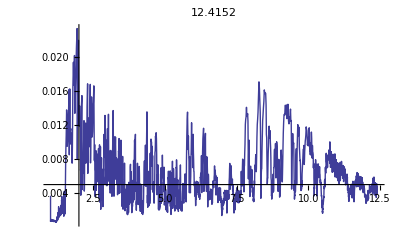

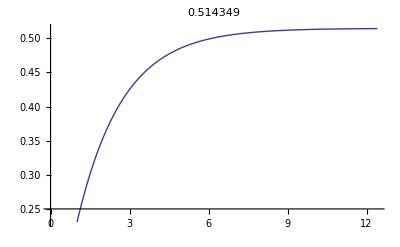

```mathematica
ltm=First[len];PrintRange[Transpose[{Drop[ltm,1],dif[ltm]}],All,PlotLabel->Last[ltm]]
st=(First[#1]==First[#2]&);
{lmp,mdp,lmvx,mdvx,lmvy,mdvy,lmvz,mdvz,lmqp,lmqvx,lmqvy,lmqvz}=Transpose[{ltm,#}]&/@Drop[len,2];
PrintRange[{#⟦1⟧/3,√(#⟦2⟧)}&/@(lmqvx+lmqvy+lmqvz),Automatic,PlotLabel->√((lmqvx+lmqvy+lmqvz)⟦-1,-1⟧)]
```

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,10^Log[10,#⟦2⟧]}&,{lmvx,lmvy,lmvz,lmp},{2}],
{"Maximum of vr","Maximum of vϕ","Maximum of vz","Maximum of p"}}]
```

```mathematica
Fit[{First[#],Log[Last[#]]}&/@Take[lmvy,All],{1,λ},λ]
```

```mathematica
MapThread[PrintRange[#1,Automatic,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,#⟦2⟧]}&,{lmqvx,lmqvy,lmqvz,lmqp},{2}],{"Mean quadratic of vr","Mean quadratic of vϕ","Mean quadratic of vz","Mean quadratic of p"}}]
```

```mathematica
MapThread[PrintRange[#1,All,PlotLabel->#2]&,{Map[{#⟦1⟧,Log[10,(#⟦2⟧)/(#⟦1⟧)]}&,Rest/@{mdvx,mdvy,mdvz,mdp},{2}],{"Maximum difference of vr","Maximum difference of vϕ","Maximum difference of vz","Maximum difference of p"}}]
```

### Нахождение предельных значений

```mathematica
PrintRange[{#⟦1⟧,Log[E,#⟦2⟧]}&/@Take[lmvx,160]]
```

```mathematica
Fit[{#⟦1⟧,Log[E,#⟦2⟧]}&/@Take[lmvx,160],{1,x},x]
```

```mathematica
PrintRange[dif[lmp],Automatic]
```

```mathematica
PrintRange[lmvx,{0.005449,0.0065}]
```

```mathematica
PrintRange[lmvy,{0.99474,0.99475}]
```

```mathematica
PrintRange[lmvz,{0.005449,0.0065}]
```

```mathematica
PrintRange[{First[#],√Last[#]}&/@lmqvy,{0.52142,0.52143}]
```

```mathematica
mvz-ListLimit[Select[lmvz,(25<First[#]<40)&],ApproximationReport->{HoelderInterval,LimitPlot,HoelderError,MaxError,Shift},CutValues->False]
```

abscisses was shifted on -24.9157

HoelderCI={0.00411362,0.00411655}

HoelderError=2.92732×10^-6

3.88936×10^-8

```mathematica
ListLimit[Select[lmqvz,(25<First[#]<40)&],ApproximationReport->{HoelderInterval,HoelderError,MaxError,Shift},CutValues->False]
```

abscisses was shifted on -24.9724

HoelderCI={2.82737×10^-6,2.82737×10^-6}

HoelderError=1.70345×10^-12

2.82737×10^-6

```mathematica
√(4.977368517344871*^-11)
```

7.05505×10^-6

```mathematica
-Subtract@@{0.995648,0.995649}
```

1.×10^-6

## Чтение снимков

```mathematica
Remove[PrintInfo];
```

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->2];
```

```mathematica
out=.;ReadBinarySnapFiles["screw",".bak",5,out,PrintInfo->None];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->2];
{p,vx,vy,vz,nut}=out;
```

```mathematica
out=.;ReadBinarySnapFile["screw_64_32564.snp",3,out,PrintInfo->Debug];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->2];
{vx,vy,vz}=Take[out,{2,4}-1];
```

{2,16,2}

{64.0006,32564,64,64,64,40.}

Length of read from binary=2772480 and size of it=11089920 bytes

ghost=3

```mathematica
{p,vx,vy,vz,nut}=ReadTextSnapFile["screw_64_6592.snp",5,PrintInfo->Automatic];
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,2},NumberOfRefs->2];
Max[Abs[GetInner[divd[{vx,vy,vz},ghost]]]]
(*Print[bounds];*)
```

Выделение внутренней области

```mathematica
GetInner[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(node/.b_:>BitAnd[b,8])/8#&/@Transpose[ar]],2,(node/.b_:>BitAnd[b,8])/8 ar,_,$Failed]]
```

```mathematica
GetVacuum[ar_?ArrayQ]:=Block[{b},Switch[Length[Dimensions[ar]],3,Transpose[(1-(node/.b_:>BitAnd[b,8])/8)#&/@Transpose[ar]],2,(1-(node/.b_:>BitAnd[b,8])/8)ar,_,$Failed]]
```

```mathematica
{vxs,vys,vzs,ps,nuts}=GetInner/@{vx,vy,vz,p,nut};
```

```mathematica
Max[Abs[GetInner@#]]&/@{vx,vy,vz,p}
```

{5.426×10^-17,0.99855,1.4157×10^-16,1}

```mathematica
Max[Abs[#]]&/@{vx,vy,vz,p}
```

{0.250679,1.00854,0.250679,Abs[p]}

```mathematica
Union@Flatten@nut
```

```mathematica
{#⟦2⟧,#⟦-1⟧}&@Union[Flatten[out[[1]]]]
```

### Трёхмерные (и близкие) графики

```mathematica
Manipulate[Block[{ar=GetInner[p][[All,ny,All]],vals},
vals=Select[Union@Flatten@p,#≠0&];
ListContourPlot[Transpose[ar],Contours->20,PlotLabel->{Min[vals],Max[vals]}]
],{ny,1,Length[Transpose[vy]],1}]
```

```mathematica
dd=GetInner[divd[{vx,vy,vz},ghost-1]];
```

```mathematica
ListContourPlot[Transpose[Cut3D[dd,2,ghost+10]],InterpolationOrder->1,PlotRange->All,ColorFunction->GrayLevel]
```

```mathematica
Max[Abs[GetInner[divd[{vx,vy,vz},ghost]]]]
```

```mathematica
Max@Abs[(#-Reverse[#])&@Transpose[Cut3D[vy,2,5]]]
```

```mathematica
ListDensityPlot[Cut3D[vy,1,3],PlotRange->All,InterpolationOrder->0]
```

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,3]],PlotRange->All,DisplayFunction->Identity]&,{vx,vy,vz,p}]
```

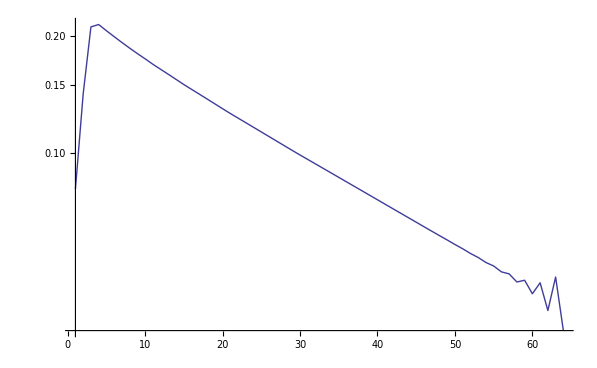

```mathematica
ListLogPlot[WithoutFict[Max/@(Flatten/@Transpose[vz])],Joined->True,PlotRange->All]
```

```mathematica
PrintRange[dif[Transpose[(WithoutFict/@{coor⟦2⟧,Max/@(Flatten/@Transpose[vx])})]]]
```

```mathematica
ListContourPlot[vx⟦10;;15,20,10;;20⟧,PlotRange->Automatic]
```

```mathematica
ListContourPlot[WithoutFict@Transpose[Cut3D[p,1,8]]/.{0->1},PlotRange->All,InterpolationOrder->None,ContourLabels->False]
```

```mathematica
ListPlot3D[Cut3D[GetInner@vy,2,67],PlotRange->All,InterpolationOrder->1]
```

```mathematica
ListContourPlot[Transpose[Cut3D[GetInner@vy,2,ghost+2]],PlotRange->Automatic,InterpolationOrder->1,Contours->20]
```

```mathematica
Options[DrawSection]
```

{PointOfSections→{1.25664,0.1+Mean[bounds⟦3⟧],Mean[bounds⟦1⟧]},AspectRatio→1,ColorFunction→(Hue[#1/1.5]&),PlotLabel→Automatic,OnlySection→False}

```mathematica
<<ACPackages`ACGraphics`
```

```mathematica
DrawSection[WithoutFict@vx,WithoutFict@vy,WithoutFict@vz,PointOfSections->{4.5,0,0},OnlySection->True]
```

```mathematica
grs=Table[DrawSection[vx,vy,vz,PointOfSections->{i,0.,0.},OnlySection->True],{i,0,2π,π/10}];
```

```mathematica
ListAnimate[grs]
```

```mathematica
PrintRange[Max/@Flatten/@WithoutFict@Transpose[vy]]
```

```mathematica
ListStreamPlot[Transpose[Cut3D[#,2,ghost+20]&/@{vx,vz},{3,1,2}]]
```

```mathematica
Manipulate[ListStreamPlot[Transpose[GetInner[Cut3D[#,2,ny]]&/@{vx,vz},{3,1,2}]],{ny,1,Dimensions[vx]⟦2⟧,1}]
```

```mathematica
vyshift=dif@Transpose[WithoutFict/@{coor⟦1⟧,vy[[All,⌊Length[Transpose[vy]]/2⌋,⌊Length[Transpose[vy]]/2⌋]]}];
PrintRange[vyshift]
FindRoot[Interpolation[vyshift][r],{r,-0.2,0.2}]
```

```mathematica
With[{nyz=35},
{PrintRange[vy⟦nyz,All,nyz⟧],
PrintRange[p⟦nyz,All,nyz⟧]}
]
```

### Разное

```mathematica
{mvx,mvy,mvz}=Max/@{vxs,vys,vzs}
```

{0,0.99951,0}

```mathematica
kappa=0.25;
```

#### Разные энергетические величины

```mathematica
(Nest[Total,(1+coor[[1]]kappa)#^2,3]&/@{vxs,vys,vzs})(Times@@(Last[#]-First[#]&/@coor))/(Times@@Dimensions[vxs])
```

{0.000133311,1.91119,0.0000445724}

```mathematica
{Evx,Evy,Evz}=(Nest[Total,WithoutFict[(1+coor[[1]]kappa)#^2],3]&/@{vxs,vys,vzs})(Times@@(Last[#]-First[#]&/@WithoutFict/@coor))/(Times@@(Dimensions[vxs]-2ghost))
```

{0.0000491437,0.70454,0.0000164312}

```mathematica
√Mean[Flatten[WithoutFict[(1+coor[[1]]kappa)#^2]]]&/@{vxs,vys,vzs}
```

{0.00435428,0.521357,0.00251777}

```mathematica
√Mean[Select[Flatten[WithoutFict[(1+coor[[1]]kappa)#^2]],(#>0&)]]&/@{vxs,vys,vzs}
```

```mathematica
√(Total[Flatten[WithoutFict[(1+coor[[1]]kappa)#^2]]]&/@{vxs,vys,vzs}/(Total[Flatten[(node/.b_:>0/;b≠8)/8]](Dimensions[vxs]⟦2⟧-2ghost)))
```

```mathematica
{qvx,qvy,qvz}=√(Total[Flatten[WithoutFict[(1+coor[[1]]kappa)#^2]]]&/@{vxs,vys,vzs}/(Total[Flatten[(node/.b_:>0/;b≠8)/8]](Dimensions[vxs]⟦2⟧-2ghost)))
```

```mathematica
ps=(node/.b_:>0/;b≠8)/8(ps-Mean[Select[Flatten[ps],#≠0&]]);
```

```mathematica
vys=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@vy),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@vys];
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

#### SectionAverage

```mathematica
ListDensityPlot[Transpose[SectionAverage[vx,2,ShowDeviation->True,DeviationNorm->0]]]
```

0-norm of arrays deviation=8.18182×10^-9

```mathematica
PrintRange[WithoutFict[SectionAverage[vz,2,ShowDeviation->True,DeviationNorm->0][[67]]]]
```

```mathematica
{Max[#],Min[#]}&[SectionAverage[vx,2][[34]]]
```

{0.0018038,-0.0013536}

```mathematica
ListPlot3D[Transpose[SectionAverage[vx,2,ShowDeviation->True,DeviationNorm->0]]]
```

```mathematica
profil=SectionAverage[vy,2]⟦34⟧//WithoutFict;
```

```mathematica
First[Max[profil](30/5.5^2)^-1 Table[(i(11-i))/5.5^2,{i,10}]]
```

0.329827

```mathematica
First[profil]
```

0.032742

```mathematica
PrintRange[(dif[profil] 15^2//dif)+0.5];
```

```mathematica
PrintRange[(profil)];
PrintRange[Max[profil](30/5.5^2)^-1 Table[(i(11-i))/5.5^2,{i,10}]];
```

```mathematica
Options[SectionAverage]={ShowDeviation->False,DeviationNorm->0};
SectionAverage[mat_,dir_:2,opts___]:=Block[
{transp=Transpose[mat,Insert[Rest[Range[Depth[mat]-1]],1,dir]],
aver,
showdisp=ShowDeviation/.{opts}/.Options[SectionAverage],
dispord=DeviationNorm/.{opts}/.Options[SectionAverage]},
aver=Mean[transp];
If[showdisp,
If[dispord==0,Print[dispord,"-norm of arrays deviation=",(Max[Abs[(#-aver)&/@transp]])],
Print[dispord,"-norm of arrays deviation=",(Total[Flatten[((#-aver)&/@transp)^dispord]]/Times@@Dimensions[transp])^(1/dispord)]
]];
Return[aver];
];
```

```mathematica
{vxss,vyss,vzss}=SectionAverage/@{vxs,vys,vzs};
```

```mathematica
SectionAverage[p,2,ShowDeviation->True,DeviationNorm->0];
```

0-norm of arrays deviation=0.0000769231

```mathematica
{vxss,vyss,vzss}=SectionAverage[#,2,ShowDeviation->True]&/@{vx,vy,vz};
```

#### DrawSection

```mathematica
Show[gds=ReadDrawSection["pumpflow_2_1993.snp",Global`Text,5,{2,3,4},PointOfSections->{0.1,0.1,0.1}],DisplayFunction->$DisplayFunction]
```

{1,1,2}

{2.00018,1993,20,20,20,10.}

ghost=3

```mathematica
(#[[2]])/(#[[1]])&[Max[Abs[#]]&/@{vx,vy,vz}]
```

423.044

```mathematica
Show2x[ListPlot3D[Transpose[Cut3D[#,2,7]],PlotRange->All,DisplayFunction->Identity]&,{vxs,vys,vzs,p}]
```

```mathematica
Show2x[ListContourPlot[Transpose[Cut3D[#,2,7]],PlotRange->All,DisplayFunction->Identity]&,{vxs,vys,vzs,p}]
```

```mathematica
Export["temp.gif",PrintRange[Transpose[{coor[[1]],Cut3D[Cut3D[vy,2],2,35]/(coor[[1]]0+1)}],All,PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->900];
```

```mathematica
Export["vstream.gif",ListContourPlot[Cut3D[vys],PlotLabel->"Angular velocity"],ImageResolution->80,ImageSize->700];
```

### Рисование поверхностей

```mathematica
{vx,vy,vz}=WithoutFict/@{vx,vy,vz};
```

```mathematica
mx=Max[vphi]
gh=ListContourPlot3D[Transpose[vphi],Contours->{-1,1}mx/4,ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{z,y,x},DataRange->bounds]
```

0.25047

```mathematica
mx=Max[helicity]
gh=ListContourPlot3D[Transpose[helicity,{1,2,3}],Contours->{-1,1}mx/2,ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{x,y,z},DataRange->bounds]
```

18.8797

```mathematica
Export["hel.eps",gh,ImageSize->300];
```

### Интерполированные графики

```mathematica
{vxi,vyi,vzi,pi,nuti}=ListInterpolation[#,{{Min[coor⟦1⟧],Max[coor⟦1⟧]},{Min[coor⟦2⟧],Max[coor⟦2⟧]},{Min[coor⟦3⟧],Max[coor⟦3⟧]}},InterpolationOrder->1]&/@{vxs,vys,vzs,p,nut};
```

```mathematica
Show2x[DensityPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},DisplayFunction->Identity]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
Show2x[ContourPlot[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotLabel->"Max="<>ToString[Max[#]]<>"; Min="<>ToString[Min[#]],Contours->20,DisplayFunction->Identity,PlotRange->All,FrameTicks->{CutList[Transpose[{Range[Length[coor⟦1⟧]],coor⟦1⟧}],10],CutList[Transpose[{Range[Length[coor⟦3⟧]],coor⟦3⟧}],10],None,None},Axes->Automatic,AxesOrigin->{1,0}]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
Show2x[Plot3D[If[(z-Mean[bounds⟦3⟧])^2+(r-Mean[bounds⟦1⟧])^2≤(bounds⟦1,2⟧-bounds⟦1,1⟧)/2,#,0],{r,bounds⟦1,1⟧,bounds⟦1,2⟧},{z,bounds⟦3,1⟧,bounds⟦3,2⟧},PlotRange->All,DisplayFunction->Identity]&,{vxi[r,0,z],vyi[r,0,z],vzi[r,0,z],pi[r,0,z]}]
```

```mathematica
gds=DisplayTogetherArray[SectionRZ[vxi,vyi,vzi,0.2 π],SectionRΦ[vxi,vyi,vzi,Mean[bounds⟦3⟧],AspectRatio->Automatic],SectionΦZ[vxi,vyi,vzi,Mean[bounds⟦1⟧],AspectRatio->Automatic],Spacings->Scaled[0.]];
```

```mathematica
Show[gds=DrawSection["pumpflow64x64x64Re=1rc=4.snp",5],DisplayFunction->$DisplayFunction]
```

```mathematica
Export["fieldRe=1rc=4.gif",gds,ImageResolution->80,ImageSize->900];
```

## Построение графиков вдоль снэпов

### Подготовка

```mathematica
ghost=3;
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,1},NumberOfRefs->2];
```

#### Старое (анимация давления)

```mathematica
dr=ReadList["debug"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
node=Clue[nm,2];
Off[Set::write];Off[General::spell1];
ReadPressure[iter_]:=Block[{i},
Clear[dumpRead,pm,p,ps];
dumpRead=ReadList["runtest1_"<>ToString[iter]<>".snp"];
{t,count,np,n1,n2,n3,Rey}=Take[dumpRead,7];dumpRead=Drop[dumpRead,7];
{vxm,vym,vzm,pm,nutm}=Transpose[Partition[dumpRead,5]];
p=First[Fold[Map[Function[m,Clue[m,#2]],Partition[#1,np⟦#2⟧],{1}]&,pm,{1,2,3}]];
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
Return[√Mean[Select[Flatten[#],Positive]]&/@(ps^2)];
];
```

```mathematica
lpres=Table[PrintRange[(#-Mean[#])&@ReadPressure[niter],{-0.5,0.7},PlotLabel->niter],{niter,100,300,100}];
```

```mathematica
ldifpres=Table[PrintRange[dif[ReadPressure[niter]],{-0.5,0.5},PlotLabel->niter],{niter,100,14200,100}];
```

```mathematica
Export["pressure.gif",lpres];
```

```mathematica
n2=20;
```

```mathematica
ps=Table[(node/.b_:>0/;b≠8)/8(#[[i]]&/@p),{i,ghost+1,n2+ghost}];
PrintRange[Mean[Mean[#]]&/@ps]
```

```mathematica
Do[SectionRZ[π i/100],{i,10,200}];
```

```mathematica
ReadSection[iter_,nproc_Integer:1]:=Block[{dump,str=ToString[iter]},
(*While[StringLength[str]<5,str="0"<>str];*)
(*{p,vx,vy,vz,nut}=ReadTextSnapFile["screw_"<>ToString[nproc]<>"_"<>str<>".snp",3,PrintInfo->None];*)
out=.;ReadBinarySnapFile["screw_"<>ToString[nproc]<>"_"<>str<>".snp",3,out,PrintInfo->None];{vx,vy,vz}=out;
If[!NameQ[coor]∨Length[coor]=!=3∨(Length/@coor)≠Dimensions[vx],
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{2,16,2},NumberOfRefs->2]];
(*Return[{Bx,By,Bz}];*)
]
```

```mathematica
nums=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]]&/@FileNames["*.snp"]]
{nproc}=Union[ToExpression[First[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$2"]]]&/@FileNames["*.snp"]]
```

{2712,4417,6266,8067,10003,11974,13870,15796,17742,19701,21840,32564,32753,35091,37440,39583,41999,44457,46942,49143,51679,54269,56870,59145,61841,64606,66917,69819,72779,75914,78285}

{64}

```mathematica
ReadZipSnap[fname_]:=Block[{fn,iter,nproc,res=Null},
If[!StringFreeQ[fname,{".gz",".bz2"}],
fn=StringReplace[fname,{".gz"->"",".bz2"->""}];
Export[fn,Import[fname],"Text"],
fn=Import[fname];
Export[fn,Import[fname,fn],"Text"]
];
{iter,nproc}=ToExpression[First[StringCases[fname,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->{"$3","$2"}]]];
ReadSection[iter,nproc]
(*res=ReadSnapHeader[fn];*)
(*Close[fn];*)
(*DeleteFile[fn];
res*)
]
```

```mathematica
ReadZipSnap/@FileNames["*.snp*"]
```

```mathematica
ReadZipSnap["pumpflow_64_6000.snp.gz"]
```

{1.07141,6000,{2,16,2},{16,128,16},1.}

```mathematica
nums=CutList[nums,20];
```

```mathematica
nums=Take[nums,20];
```

```mathematica
nums=Select[nums,(#>20000&)];Length[nums]
```

46

```mathematica
nums=Select[nums,Mod[#,15]==0&];Length[nums]
```

117

### Чтение

```mathematica
Export["divert"<>ToString[#]<>".gif",(ReadSection[#,nproc];DrawSection[vx,vy,vz,PointOfSections->{2,0,0}])]&/@nums;
```

```mathematica
{coor,bounds,node}=ReadAuxFiles[{"coord","node"},ShiftVector->{0,0,0},ProcDistrib->{1,2,1},NumberOfRefs->2];phi=Outer[ArcTan,coor[[1]],coor[[3]]];
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{vx,vy,vz}],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
res={};nums=SortBy[FileNames["*.snp*"],ToExpression[StringCases[#,RegularExpression["([^_]+?)_([^_]+?)_([^\\.]+?)\\.(.*?)"]->"$3"]]&];
Monitor[Do[ReadZipSnap[nums⟦i⟧];AppendTo[res,{vx,vy,vz,p}],{i,Length[nums]}],
{PrintRange[p⟦7,All,7⟧,All,PlotLabel->tsec],
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi,All,PlotLabel->tsec]}]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{vx,vy,vz,p}],{i,Length[nums]}],{ListContourPlot[Cut3D[Last[res]⟦2⟧,1,7],PlotRange->All,PlotLabel->nums⟦i⟧],PrintRange[res⟦-1,2,7,All,7⟧,All,PlotLabel->tsec]}]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,DrawSection[vx,vy,vz,PointOfSections->{2,0,0},OnlySection->True]],{i,Length[nums]}],Last[res]]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,Total[MapThread[Times,{{vx,vy,vz},rotc[vx,vy,vz,ghost]}]]],{i,Length[nums]}],{infos[[i]],ListLogPlot[Mean/@Flatten/@Transpose[Last[res]]]}]
```

```mathematica
res={};Monitor[Do[ReadSection[nums⟦i⟧,nproc];AppendTo[res,{
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];ListLogPlot[Max/@Flatten/@WithoutFict@vphi,PlotLabel->tsec],
ListLogPlot[Mean/@Flatten/@WithoutFict@vphi,PlotLabel->tsec],
PrintRange[WithoutFict@vy⟦19,All,19⟧,Automatic,PlotLabel->tsec],
DrawSection[vx,vy,vz,PointOfSections->{2,0,0}]}
],{i,Length[nums]}],Prepend[Most[Last[res]],nums[[i]]]]
```

### Просмотр

```mathematica
Dimensions[res]
```

{31,70,70,70}

```mathematica
ListAnimate[res[[All,4]]]
```

```mathematica
mean=Mean@res;
```

```mathematica
DrawSection[mean⟦1⟧,mean⟦2⟧,mean⟦3⟧,PointOfSections->{2,0,0},OnlySection->True]
```

```mathematica
vphi=Table[mean[[1,All,ny,All]]Sin[phi]-mean[[3,All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[mean[[1,All,ny,All]]Cos[phi]+mean[[3,All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
DrawSection[Sequence@@res[[17]],PointOfSections->{0.1,0,0}]
```

```mathematica
PrintRange[Log/@Max/@Flatten/@WithoutFict@vphi]
PrintRange[Log/@Max/@Flatten/@WithoutFict@vrho]
```

```mathematica
ListContourPlot[Transpose[mean⟦4,All,6⟧]/.{0->1},PlotRange->All]
```

```mathematica
With[{nxz=6},Manipulate[{nums⟦i⟧,PrintRange[WithoutFict@res⟦i,2,nxz,All,nxz⟧,1+1{-1,1},PlotLabel->"stream velocity"],PrintRange[WithoutFict@res⟦i,4,nxz,All,nxz⟧,1+0.5{-1,1},PlotLabel->"pressure"]},{i,1,Length[res],1}]]
```

```mathematica
Manipulate[{nums⟦i⟧,PrintRange[WithoutFict@(res⟦i,1,20,ghost+1,All⟧),{0,1},PlotLabel->"stream velocity"]},{i,1,Length[res],1}]
```

```mathematica
Save["Re1evol.m",res]
```

```mathematica
ListAnimate[grs]
```

```mathematica
Show[Drop[grs,2]]
```

```mathematica
Manipulate[{nums⟦i⟧,ListContourPlot[Transpose[res⟦i,3,All,All,28⟧],PlotRange->All,PlotLabel->infos⟦i⟧,PerformanceGoal->"Quality"]},{i,1,Length[res],1}]
```

```mathematica
Manipulate[{DrawSection[res⟦i,1⟧,res⟦i,2⟧,res⟦i,3⟧,PointOfSections->{1,0,0},OnlySection->True],ListContourPlot[Transpose[res⟦i,4,All,5⟧]/.{0->1},PlotRange->All,PlotLabel->nums⟦i⟧,PerformanceGoal->"Quality"]},{i,1,Length[res],1}]
```

```mathematica
Manipulate[DrawSection[res⟦i,1⟧,res⟦i,2⟧,res⟦i,3⟧,PointOfSections->{2,0,0},OnlySection->False],{i,1,Length[res],1}]
```

```mathematica
PrintRange[Transpose[Table[{#⟦2⟧,#⟦-1⟧}&@Union[Flatten[res⟦i,-1⟧]],{i,Length[res]}]]]
```

```mathematica
ListLinePlot[Log@Transpose[Map[Max[Abs[#]]&,res,{2}]]⟦4⟧]
```

```mathematica
Do[Export["divert"<>ToString[nums[[i]]]<>".gif",res⟦i,-1⟧,ImageSize->700],{i,Length[res]}];
```

```mathematica
Export["divert.gif",Last/@res]
```

```mathematica
Manipulate[res⟦i,1;;2⟧,{i,1,Length[res],1}]
```

## Всё со спиральностью

```mathematica
Maximize[{r(1-r^2),0<r<1},r]
```

{2/(3 √3),{r→1/(√3)}}

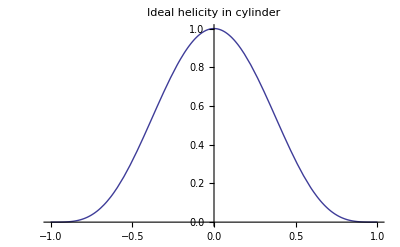

```mathematica
Plot[(1-x^2)^2,{x,-1,1},PlotLabel->"Ideal helicity in cylinder"]
```

```mathematica
Clear[DecrHel];
DecrHel[vx_,vx_,vz_,range_:{40,50}]:=DecrHel[Transpose[Total[MapThread[Times,{{vx,vy,vz},rotd[vx,vy,vz,ghost]}]]],range]
DecrHel[hel_,range_:{40,50}]:=Block[{cr=Outer[List,Sequence@@coor]⟦All,1,All,1⟧,list},
If[Length[Dimensions[hel]]>2,
If[Dimensions[cr]≠Rest[Dimensions[hel]],Return["Сетка не совпадает"]];
list=If[Total[Flatten[cr]]==0.,WithoutFict[Mean/@(Flatten/@hel)],WithoutFict[Total[Flatten[cr#]]/Total[Flatten[cr]]&/@hel]],
list=hel;
];
If[Length[Dimensions[list]]<2,list=Transpose[{WithoutFict[coor⟦2⟧],list}]];
D[Fit[Take[{First[#],Log[Last[#]]}&/@list,range],{1,z},z],z]
]
```

### Просмотр снимка

```mathematica
phi=Outer[ArcTan,coor[[1]],coor[[3]]];
vphi=Table[vx[[All,ny,All]]Sin[phi]-vz[[All,ny,All]]Cos[phi],{ny,Dimensions[vx][[2]]}];
vrho=Table[vx[[All,ny,All]]Cos[phi]+vz[[All,ny,All]]Sin[phi],{ny,Dimensions[vx][[2]]}];
```

```mathematica
Manipulate[{ListContourPlot[vphi[[ny]],PlotRange->Automatic],ListContourPlot[vrho[[ny]],PlotRange->Automatic]},{ny,1,Length[vy],1}]
```

```mathematica
Manipulate[{ListPlot3D[vphi[[ny]],PlotRange->Automatic],ListPlot3D[vrho[[ny]],PlotRange->Automatic]},{ny,1,Length[vy],1}]
```

```mathematica
ListLogPlot[Mean/@Flatten/@vphi]
```

```mathematica
Fit[Take[Transpose[{coor[[2]],Log/@Mean/@Flatten/@vphi}],{10,40}],{1,z},z]
```

-2.43246-0.314062 z

```mathematica
PrintRange[Transpose[(WithoutFict/@{coor⟦2⟧,Log/@Max/@Flatten/@vphi})]]
PrintRange[Log/@Max/@Flatten/@vrho]
```

```mathematica
ListPlot[dif[Transpose[(WithoutFict/@{coor⟦2⟧,Log/@Max/@Flatten/@vphi})]]]
```

```mathematica
With[{ny=6},{ListContourPlot[vphi[[ny]],PlotRange->All],ListContourPlot[vrho[[ny]],PlotRange->All]}]
```

```mathematica
helicity=Total[MapThread[Times,{{vx,vy,vz},rotc[vx,vy,vz,ghost]}]];
```

```mathematica
helicity=rotd[vx,vy,vz,ghost][[2]];
```

```mathematica
cr=Outer[List,Sequence@@coor]⟦All,1,All,1⟧;
```

```mathematica
ListLogPlot[Total[Flatten[cr#]]/Total[Flatten[cr]]&/@Transpose[res[[1]]]]
```

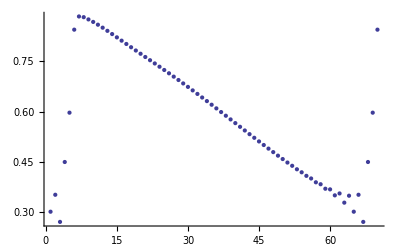

```mathematica
ListPlot[helicity[[35,All,35]]]
```

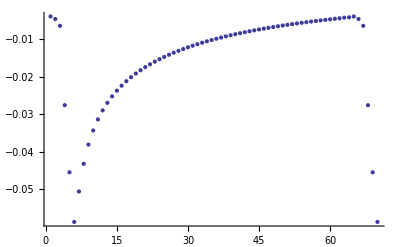

```mathematica
ListPlot[Mean/@Flatten/@Transpose[helicity]]
```

```mathematica
Fit[Take[Transpose[{coor[[2]],Log/@Mean/@Flatten/@Transpose[helicity]}],{20,50}],{1,z},z]
```

-1.96554-1.74788 z

```mathematica
ListPlot3D[helicity[[All,ghost+10]],PlotRange->All]
```

```mathematica
Manipulate[ListContourPlot[GetInner@helicity[[All,ny]],PlotRange->All],{ny,1,Dimensions[vx]⟦2⟧,1}]
```

```mathematica
With[{num=1},helicity=Total[MapThread[Times,{res[[num]],rotd[Sequence@@res[[num]],ghost]}]];
Print[ListLogPlot[Mean/@Flatten/@Transpose[helicity]]];
Print[ListPlot[dif@Transpose[{coor[[2]],Log/@Mean/@Flatten/@Transpose[helicity]}]]];
]
```

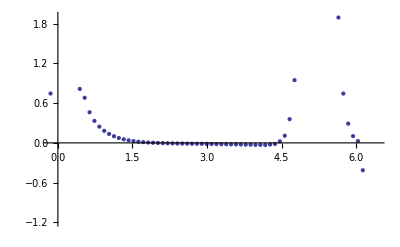

```mathematica
ListPlot[dif@dif@Transpose[{coor[[2]],Log/@Mean/@Flatten/@Transpose[helicity]}]]
```

### Универсальный просмотрщик

```mathematica
list3d=Transpose[vx];
```

```mathematica
list3d=Transpose[helicity];
```

```mathematica
ACPackages`ACListNumerics`Private`coor=coor;
list3d=Transpose[Total[MapThread[Times,{{vx,vy,vz},rotc[vx,vy,vz,ghost]}]]];
```

```mathematica
list3d=Transpose[rotd[vx,vy,vz,ghost][[2]]];
```

```mathematica
list=WithoutFict[Max/@(Flatten/@list3d)];
```

```mathematica
cr=Outer[List,Sequence@@coor]⟦All,1,All,1⟧;
```

```mathematica
If[Total[Flatten[cr]]==0.,
Print["descartes averaging"];list=WithoutFict[Mean/@(Flatten/@list3d)],
Print["cylindrical averaging"];list=WithoutFict[Total[Flatten[cr#]]/Total[Flatten[cr]]&/@list3d]
];
```

cylindrical averaging

```mathematica
listc=Transpose[{WithoutFict[coor⟦2⟧],list}];
```

```mathematica
listc=MovingAverage[listc,3];
```

```mathematica
ListLogPlot[Abs[list],Joined->False,PlotRange->Automatic]
```

```mathematica
ListPlot[dif@(Abs[list]^-1),Joined->False,PlotRange->Automatic]
```

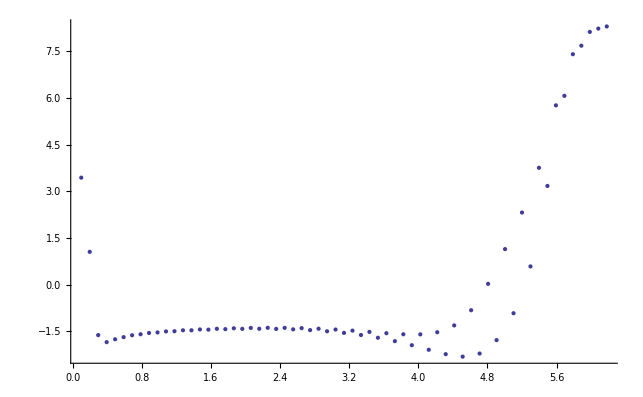

```mathematica
ListPlot[dif[{First[#],Log[Abs@Last[#]]}&/@listc],PlotRange->Automatic]
```

```mathematica
Fit[Take[{First[#],Log[Last[#]]}&/@listc,{45,55}],{1,z},z]//Chop
```

-1.6149-0.284676 z

```mathematica
Manipulate[PrintRange[list3d[[ny,⌊(Dimensions[list3d]⟦3⟧)/2⌋]]],{{ny,ghost},1,Length[list3d],1}]
```

```mathematica
With[{ny=6},ListPlot3D[list3d[[ny]],PlotRange->All]]
```

```mathematica
Manipulate[ListPlot3D[Transpose[list3d[[ny]]],PlotRange->All],{{ny,ghost},1,Length[list3d],1}]
```

```mathematica
With[{ny=6},ListContourPlot[list3d[[ny]],PlotRange->Automatic]]
```

```mathematica
Manipulate[ListContourPlot[Transpose[list3d[[ny]]],PlotRange->All],{{ny,ghost},1,Length[list3d],1}]
```

```mathematica
list3d=Transpose[(WithoutFict[GetInner@(Transpose[list3d])])];
```

```mathematica
mx=Max[list3d]
gh=ListContourPlot3D[Transpose[list3d],Contours->{-1,1}mx/2,ContourStyle->{Directive[Yellow,Opacity[0.8]],Directive[Pink,Opacity[0.8]]},BoxRatios->Automatic,Mesh->False,AxesLabel->{z,y,x},DataRange->bounds]
```

0.766657

### Из прочитанных снимков

```mathematica
With[{nxz=11},Manipulate[{vphi=Table[res⟦i,1,All,ny,All⟧Sin[phi]-res⟦i,3,All,ny,All⟧Cos[phi],{ny,Dimensions[res]⟦4⟧}];PrintRange[Log/@Max/@Flatten/@vphi,All,PlotLabel->nums⟦i⟧],
PrintRange[res⟦i,2,nxz,All,nxz⟧,Automatic,PlotLabel->nums⟦i⟧],PrintRange[res⟦i,4,nxz,All,nxz⟧,All,PlotLabel->nums⟦i⟧]},{i,1,Length[res],1}]
]
```

```mathematica
grs2=Table[(vphi=Table[res⟦i,1,All,ny,All⟧Sin[phi]-res⟦i,3,All,ny,All⟧Cos[phi],{ny,Dimensions[res]⟦4⟧}];PrintRange[Log[Max/@Flatten/@vphi],All,PlotLabel->Last@ReadSnapHeader["screw_32_"<>ToString[nums⟦i⟧]<>".snp"]]),{i,1,Length[res]}];
```

```mathematica
ListAnimate[Show[#,PlotRange->{-3,0},AxesOrigin->{0,0}]&/@grs2]
```

```mathematica
grs=Table[(vphi=Table[res⟦i,1,All,ny,All⟧Sin[phi]-res⟦i,3,All,ny,All⟧Cos[phi],{ny,Dimensions[res]⟦4⟧}];PrintRange[1/2 Log/@Mean/@Flatten/@(vphi^2),All,PlotLabel->First@ReadSnapHeader["screw_2_"<>ToString[nums⟦i⟧]<>".snp"]]),{i,1,Length[res],1}];
```

```mathematica
Save["hel_evol.m",grs]
```

```mathematica
With[{n=27516},list=First@ExtractList[grs2[[Position[nums,n]⟦1,1⟧]]];
Print[ListPlot[list]];
D[Log[10]Fit[Take[Transpose[{coor[[2]],Last/@list}],{10,40}],{1,z},z],z]
]
```

-0.278804

```mathematica
Manipulate[
{Show[grs2[[n]],PlotRange->{-10,0},AxesOrigin->{0,0}],D[Fit[Take[Transpose[{coor[[2]],ExtractList[grs2[[n]]]⟦1,All,-1⟧}],{s1,s2}],{1,z},z],z]},
{n,1,Length[grs2],1},{{s1,10},1,Length[First@ExtractList[First@grs2]],1},{{s2,30},1,Length[First@ExtractList[First@grs2]],1}
]
```

```mathematica
Manipulate[ListLogPlot[Mean/@Flatten/@Transpose[res⟦i⟧],PlotLabel->TableForm[{ToString@infos[[i]],func}],Prolog->(func=Fit[Take[Transpose[{coor[[2]],Log/@Mean/@Flatten/@Transpose[res⟦i⟧]}],{begin,end}],{1,z},z];Line[{{1,func/.z->coor⟦2,1⟧},{70,func/.z->coor⟦2,-1⟧}}])],{i,1,Length[res],1},{{begin,40},10,70,1},{{end,50},begin,70,1}]
```

```mathematica
Manipulate[ListPlot[dif[Transpose[{coor⟦2⟧,Log/@Mean/@Flatten/@Transpose[res⟦i⟧]}]],PlotLabel->ToString@infos[[i]],Epilog->Line[{{coor⟦2,1⟧,decrs⟦i⟧},{coor⟦2,-1⟧,decrs⟦i⟧}}]],{i,1,Length[res],1}]
```

```mathematica
decrs=DecrHel[#,{20,30}]&/@Transpose[res,{1,3,2,4}]
```

{-2.55954,-1.41134,-1.19527,-1.0609,-0.955465,-0.868987,-0.797276,-0.73757,-0.687563,-0.645491,-0.609812,-0.494768,-0.492589,-0.466089,-0.456445,-0.44743,-0.439924,-0.433675,-0.428286,-0.423805,-0.420236,-0.417438,-0.415281,-0.413679,-0.412571,-0.411894,-0.411577,-0.411556,-0.411781,-0.41221,-0.412803}

```mathematica
decrs2=Table[Append[infos[[i]],DecrHel[Transpose[res⟦i⟧],{20,30}]],{i,Length[res]}]
```

{{4.00176,2712,10.,-2.55954},{8.00079,4417,12.,-1.41134},{12.0002,6266,14.,-1.19527},{16.0018,8067,16.,-1.0609},{20.0013,10003,18.,-0.955465},{24.0003,11974,20.,-0.868987},{28.0008,13870,22.,-0.797276},{32.0012,15796,24.,-0.73757},{36.0022,17742,26.,-0.687563},{40.0014,19701,28.,-0.645491},{44.0012,21840,30.,-0.609812},{64.0006,32564,40.,-0.494768},{64.0003,32753,42.,-0.492589},{68.0006,35091,44.,-0.466089},{72.0002,37440,46.,-0.456445},{76.0001,39583,48.,-0.44743},{80.0009,41999,50.,-0.439924},{84.0018,44457,52.,-0.433675},{88.0002,46942,54.,-0.428286},{92.0006,49143,56.,-0.423805},{96.0006,51679,58.,-0.420236},{100.001,54269,60.,-0.417438},{104.,56870,62.,-0.415281},{108.,59145,64.,-0.413679},{112.002,61841,66.,-0.412571},{116.,64606,68.,-0.411894},{120.001,66917,70.,-0.411577},{124.001,69819,72.,-0.411556},{128.001,72779,74.,-0.411781},{132.002,75914,76.,-0.41221},{136.001,78285,78.,-0.412803}}

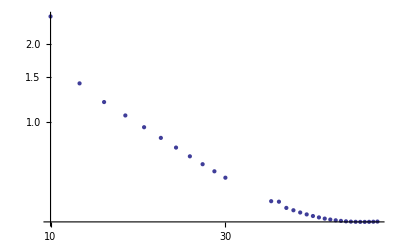

```mathematica
ListLogLogPlot[{#⟦3⟧,-#⟦4⟧}&/@decrs2]
```

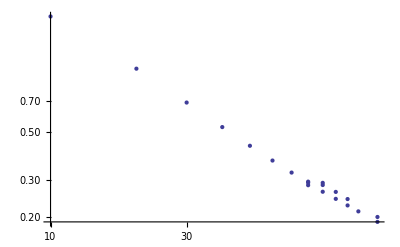

```mathematica
j
```

### Сохранение профилей

```mathematica
SetWorkDir[]
```

D:\Работа\Programs\torgrid

```mathematica
output=MapThread[{#1,#2}&,{Take[infos,20],Map[Mean[Flatten[Transpose[#]]]&,Transpose[res,{1,3,2,4}],{2}]}];
```

```mathematica
output=MapThread[{#1,Transpose[{coor⟦2⟧,#2}]}&,{Take[infos,20],Map[Mean[Flatten[Transpose[#]]]&,Transpose[res,{1,3,2,4}],{2}]}];
```

```mathematica
output=MapThread[{#1,Transpose[{coor⟦2⟧,#2}]}&,{Take[infos,31],Map[Total[Flatten[cr Transpose[#]]]/Total[Flatten[cr]]&,Transpose[res,{1,3,2,4}],{2}]}];
```

```mathematica
PutAppend[Sequence@@output,"hels.dat"]
```

```mathematica
Close["hels.dat"]
```

```mathematica
hels=ReadList["hels01.dat"];
```

```mathematica
Table[Fit[{First[#],Log[Last[#]]}&/@Take[hels⟦num,2⟧,{10,20}],{1,z},z],{num,Length[hels]}]
```

{-1.96631-2.11555 z,-1.91893-1.5523 z,-1.86939-1.36502 z,-1.8345-1.23454 z,-1.80706-1.13145 z,-1.78423-1.04726 z,-1.76455-0.977295 z,-1.74711-0.918331 z,-1.73132-0.868011 z,-1.71679-0.824597 z,-1.70326-0.786792 z,-1.64522-0.655395 z,-1.63253-0.638038 z,-1.62535-0.619919 z,-1.61489-0.60686 z,-1.60598-0.5948 z,-1.59762-0.584243 z,-1.5896-0.574861 z,-1.58189-0.566624 z,-1.5745-0.559487 z,-1.5675-0.553325 z,-1.56094-0.548008 z,-1.55479-0.543456 z,-1.54903-0.539606 z,-1.54364-0.536388 z,-1.53861-0.533735 z,-1.53392-0.53158 z,-1.52955-0.529882 z,-1.52547-0.528596 z,-1.52166-0.527685 z,-1.5181-0.527114 z}

```mathematica
Transpose[{hels[[All,1,3]]//Rationalize,-D[%,z]}]
```

{{10,2.11555},{12,1.5523},{14,1.36502},{16,1.23454},{18,1.13145},{20,1.04726},{22,0.977295},{24,0.918331},{26,0.868011},{28,0.824597},{30,0.786792},{40,0.655395},{42,0.638038},{44,0.619919},{46,0.60686},{48,0.5948},{50,0.584243},{52,0.574861},{54,0.566624},{56,0.559487},{58,0.553325},{60,0.548008},{62,0.543456},{64,0.539606},{66,0.536388},{68,0.533735},{70,0.53158},{72,0.529882},{74,0.528596},{76,0.527685},{78,0.527114}}

```mathematica
ListLogLogPlot[%]
```

```mathematica
Manipulate[ListLogPlot[hels[[num,2]],PlotLabel->hels[[num,1]],Prolog->(func=Fit[{First[#],Log[Last[#]]}&/@Take[hels⟦num,2⟧,{begin,end}],{1,z},z];Line[{{coor⟦2,1⟧,func/.z->coor⟦2,1⟧},{coor⟦2,-1⟧,func/.z->coor⟦2,-1⟧}}])],{num,1,Length[hels],1},{{begin,40},10,70,1},{{end,50},begin,70,1}]
```

## Проверки

### Совпадение при разных делениях

```mathematica
res1={};Monitor[Do[ReadSection[nums⟦i⟧,1];AppendTo[res1,{vx,vy,vz,p}],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
res2={};Monitor[Do[ReadSection[nums⟦i⟧,2];AppendTo[res2,{vx,vy,vz,p}],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
res3={};Monitor[Do[ReadSection[nums⟦i⟧,3];AppendTo[res3,{vx,vy,vz,p}],{i,Length[nums]}],nums⟦i⟧]
```

```mathematica
Map[Max[Abs[Flatten[#]]]&,res1-res3,{2}]
```

```mathematica
dump1=ReadList["pumpflow_1_2.snp"];
```

```mathematica
dump3=ReadList["pumpflow_3_2.snp"];
```

```mathematica
dump=ReadList["pumpflow.dmp"];
```

```mathematica
Dimensions/@dump
```

```mathematica
Transpose[dump3[[14,All,5]]]//TableForm
```

```mathematica
res3[[1,3,All,5]]//TableForm
```

```mathematica
ArrayPlot[(res1-res3)[[7,1,All,5]]]
```

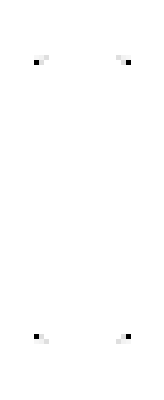

```mathematica
ArrayPlot[Transpose[dump3[[9+5,All,6]]]]
```

```mathematica
{res1[[2,1,25,6,5]],res3[[2,1,25,6,5]],dump3[[14,5,6,5]],dump1[[9,25,6,5]]}
```

{0,-1410.5,-1410.5,0}

```mathematica
dump3=ReadList["pumpflow_3_2.snp"];
```

```mathematica
With[{i=9},Transpose[(dump3[[i+5]]-0Take[dump1⟦i⟧,{20,47}])[[All,6]]]//TableForm]
```

0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4402.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4402.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -4402.6 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4402.6 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

```mathematica
Map[Max[Abs[Flatten[#]]]&,res1-res3,{2}]
```

{{0,0,0,0},{40000,0,0,0},{1.552×10^6,7.8663×10^-15,15576,71.189},{5.149×10^10,4.6405×10^-11,1.6068×10^7,28461},{1.8456×10^21,0.0067369,3.2356×10^15,1.9187×10^11},{1.8151×10^46,3.8409×10^13,4.0508×10^34,2.1017×10^25},{5.2475×10^43,1.1104×10^11,1.1711×10^32,6.076×10^22}}

```mathematica
ListPlot3D[Transpose[(res1-res3)[[2,1,All,6]]],PlotRange->All]
```

```mathematica
res3[[2,1,27,6,5]]
```

-5000

```mathematica
Union@Flatten[(res1-res3)[[2,1]]]
```

{-40000,-5000,-2003.5,-1410.5,0,1410.5,2003.5,5000,40000}

```mathematica
Dimensions[res]
```

{7,4,68,18,68}

```mathematica
Position[(res1-res3)[[2,1,All,6]],_?(Abs[#]>1&)]
```

{{25,5},{25,6},{25,63},{25,64},{26,5},{26,6},{26,63},{26,64},{27,5},{27,64},{42,5},{42,64},{43,5},{43,6},{43,63},{43,64},{44,5},{44,6},{44,63},{44,64}}

```mathematica
ArrayPlot[Sign[Transpose[(res1-res3)[[2,1,All,6]]]],PlotRange->All]
```

-Graphics-

```mathematica
res2=res;
```

### Проверка типов ячеек

```mathematica
dr=ReadList["node"];
{nm,refr,refz}=Transpose[Partition[dr,3]];
(*node=Clue[nm,2];*)
node=First[nm];
```

```mathematica
{coor,bounds,node,{rr,rz}}=ReadAuxFiles[{"coord","node","ref"},NumberOfRefs->2,ProcDistrib->{3,1,1}];
```

```mathematica
Union[Flatten[node]]
```

{4,8,12,20}

```mathematica
ListDensityPlot[node,InterpolationOrder->0]
```

```mathematica
ListDensityPlot[Transpose[BitAnd[node,8]],InterpolationOrder->0]
```

```mathematica
Transpose[node]//TableForm
```

```mathematica
Transpose[BitAnd[node,20]]//TableForm
```

```mathematica
ListDensityPlot[Transpose[BitAnd[nm[[2]],8]]]
```

```mathematica
ghost=4;
n1=First[Dimensions[node]]-2ghost
```

```mathematica
Transpose[nm[[2]]]//TableForm
```

5 | 5 | 5 | 5 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5
5 | 5 | 5 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 5 | 5 | 5
21 | 21 | 21 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 21 | 21 | 21
21 | 21 | 21 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 21 | 21 | 21
21 | 21 | 21 | 21 | 20 | 20 | 12 | 12 | 12 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 12 | 12 | 20 | 20 | 21 | 21 | 21 | 21
21 | 21 | 21 | 13 | 12 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 13 | 21 | 21 | 21
21 | 13 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 13 | 21
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
9 | 9 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 9 | 9
21 | 13 | 9 | 9 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 9 | 9 | 13 | 21
21 | 21 | 21 | 13 | 12 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 13 | 21 | 21 | 21
21 | 21 | 21 | 21 | 20 | 20 | 12 | 12 | 12 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 12 | 12 | 20 | 20 | 21 | 21 | 21 | 21
21 | 21 | 21 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 21 | 21 | 21
21 | 21 | 21 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 21 | 21 | 21
5 | 5 | 5 | 21 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 20 | 21 | 5 | 5 | 5
5 | 5 | 5 | 5 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 4 | 5 | 5 | 5 | 5

```mathematica
Transpose[node[[24;;30,2;;8]]]//TableForm
```

```mathematica
gc=Graphics[Circle[{n1/2+ghost+2 1/2,n1/2+ghost+2 1/2},n1/2]];
gc3d=ParametricPlot3D[{n1/2+ghost+1/2+n1/2 Sin[t],n1/2+ghost+1/2+n1/2 Cos[t],30},{t,0,2π},Axes->False,Boxed->False];
```

```mathematica
grnode[type_]:=ListPointPlot3D[BitAnd[node,type],ColorFunction->(Hue[1-#3]&),ViewPoint->{0,0,∞},PlotStyle->PointSize[Large]]
```

```mathematica
ArrayPlot[BitAnd[node,20]]
```

```mathematica
ArrayPlot[Table[20⌊(i-1)/20⌋,{i,60},{j,60}]+WithoutFict@rr]
```

```mathematica
Show[Graphics3D[Point[{rr[[First[#],Last[#]]]+20⌊(First[#]-1)/20⌋,rz[[First[#],Last[#]]],1}&/@Position[node,12]+1]],PlotRange->All]
```

```mathematica
Show[grnode[4],Graphics3D[Point[{rr[[First[#],Last[#]]]+20⌊(First[#]-5)/20⌋,rz[[First[#],Last[#]]],1}&/@Position[node,20]+1]],gc3d,PlotRange->All]
```

```mathematica
Show[ListPointPlot3D[Cut3D[vy,2,26],ColorFunction->(GrayLevel[#3]&),ViewPoint->{0,0,∞},PlotStyle->PointSize[Large]],gc3d,Graphics3D[Point[{rr[[First[#],Last[#]]],rz[[First[#],Last[#]]],1}&/@Position[node,20]+1]],PlotRange->All]
```

```mathematica
Show[ListPointPlot3D[node,ColorFunction->(Hue[1-#3]&),ViewPoint->{0,0,∞},PlotStyle->PointSize[Large]],gc3d,Graphics3D[Point[{rr[[First[#],Last[#]]],rz[[First[#],Last[#]]],1}&/@Position[node,20]+1]]]
```

```mathematica
ListDensityPlot[node,InterpolationOrder->0,ColorFunction->GrayLevel,PlotRange->{0,35}]
```

```mathematica
Export["cells-big.eps",Show[{ListDensityPlot[node,InterpolationOrder->0,ColorFunction->GrayLevel],gc},PlotRange->{{1,15},{1,15}}]]
```

cells-big.eps

```mathematica
DisplayTogether[ListDensityPlot[node],gc];
```

```mathematica
ListDensityPlot/@{node,rr,rz};
```

```mathematica
ListContourPlot[node]
ListContourPlot[rr]
ListContourPlot[rz]
```

### Проверка дивергенции

```mathematica
ListPlot3D[Transpose[Cut3D[GetInner@#]],PlotRange->All]&/@{PD[vx,ghost,0.2,1],PD[vx,ghost,0.2,1]+PD[vy,ghost,0.2,2]+PD[vz,ghost,0.2,3],PD[vz,ghost,0.2,3]}
```

```mathematica
dd=divd[{vx,vy,vz},ghost];
dds=GetInner[dd];
```

```mathematica
Max/@Abs/@{dd,dds}
```

{0.247128,0.00350342}

```mathematica
ListPlot3D[WithoutFict@Transpose[Cut3D[GetInner@dds,2,ghost+1]],PlotRange->All]
```

```mathematica
ListPlot3D[Transpose[Cut3D[dds,2,#]],PlotRange->All]&/@Range[Dimensions[vx]⟦2⟧]
```

```mathematica
ListPlot3D[Transpose[Cut3D[vx,2,#]],PlotRange->All]&/@Range[Dimensions[vx]⟦2⟧]
```

```mathematica
l=Monitor[Table[(ReadSection[nums⟦i⟧];Max[Abs[GetInner[divd[{vx,vy,vz},ghost]]]]),{i,Length[nums]}],{nums⟦i⟧}]
```

{0.000896198,0.000896068,0.00089607,0.00089607,0.000896115,0.0225769,0.000896107,0.000896115,0.000896113,0.000896115,0.00089607,3.60792,0.000896115,0.00089607,0.000896115,0.000896115,0.000896115,0.000896115,0.00089607,0.000896115,0.00089607,0.000896115,0.00180734,0.00178817,0.00179053,0.00179097,0.00179091,0.00179093,0.00179101,0.00179098,0.00179094,0.00179097,0.001791,0.00179101,0.00179094,0.00179093,0.001791,0.00179094,0.00179093,0.00179097,0.00179101,0.00179098,0.00281288,0.0027098,0.00297745,0.00364751,0.00479974,0.00645754,0.00948525,0.0217072,0.0437458,0.104496,0.247742,0.533909,1.14592,2.19225,3.27643,8.0703,19.6509}

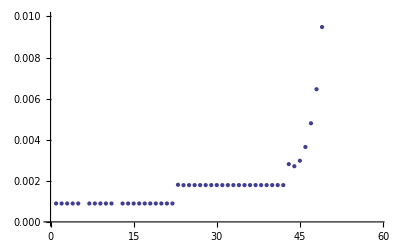

```mathematica
ListPlot[l,PlotRange->{0,0.01}]
```